### Simulation display Kristian Lindgren kristian.lindgren@chalmers.se Identity model -- simulation code Paper in PLOS-1: P. Törnberg, C. Andersson, K. Lindgren, S. Banisch - All parameter settings done in “initialize” - Simulation run by procedure “simulate” Model revised July 15, 2021.

```mathematica
(* run the model with settings in "initialize" *)
(* result dynamically displayed below *)
initialize;
simulate[500,nGlobal,nLocal];
```

```mathematica
Dynamic[ListPlot[outStrListᵀ,Joined->True,PlotRange-> Full,Frame->True,FrameLabel->{"Time","Strengths"}, PlotStyle->{{Dotted,Black},{Dashed,Black},{Dashing[{0.02,0.01}],Black},Black},LabelStyle->Directive[14,FontFamily-> "Arial"],AxesOrigin->{1,0},ImageSize->{600,400}]]
```

```mathematica
(* Illustration of strengths in a sequence of n positions *)
(* Dynamically displayed if "display=TRUE" in "initialize" *)
sampleSize=200;
sample=pop[[1;;sampleSize]];
wgtsTableN=Array[Array[0&,{nIdentity}]&,{sampleSize}];
Table[wgtsTableN[[i,sample[[i,j,1]]]]=sample[[i,j,2]],{i,1,sampleSize},{j,1,nIndIdy}];

Dynamic[BarChart[wgtsTableN,ChartStyle->colStyle,ChartLayout->"Stacked",ImageSize->{800,400},PlotRange->{0,nIndIdy},BarSpacing->{0,0}]]
```

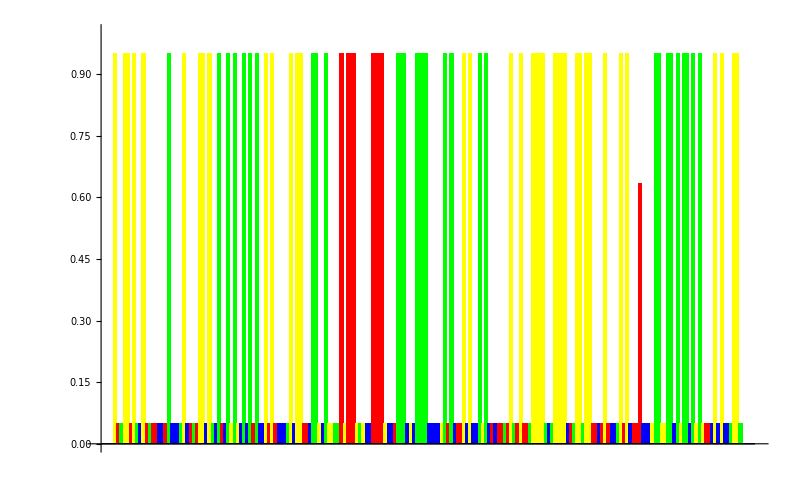

```mathematica
sampleSize=200;
sample=pop[[1;;sampleSize]];
wgtsTableN=Array[Array[0&,{nIdentity}]&,{sampleSize}];
Table[wgtsTableN[[i,sample[[i,j,1]]]]=sample[[i,j,2]],{i,1,sampleSize},{j,1,nIndIdy}];

BarChart[wgtsTableN,ChartStyle->colStyle,ChartLayout->"Stacked",ImageSize->{800,400},PlotRange->{0,nIndIdy},BarSpacing->{0,0}]
```